## Optimal Execution with Limit and Market Orders

## 8.2 Liquidation with Only Limit Orders

```mathematica
ω[t_,q_]:= ∑_(n=0)^q tλ^n/(n!)*ⅇ^(-κ*α*(q-n)^2)*(T-t)^n
ω[t_,q_]:=ⅇ^(-κ*α*q^2)/;t==T
ω[t_,q_]:=1/;q== 0
```

```mathematica
δ[t_,q_]:=1/κ*(1+Log[ω[t,q]/ω[t,q-1]])
(*
	Optimal Depth: Post LO @Price=S_t + δ 
*)
```

```mathematica
λ=50/60;
tλ=λ*ⅇ^-1;

κ=100.0;
T=60;
α=10^-3;
𝒩=5;
σ=0.01;
```

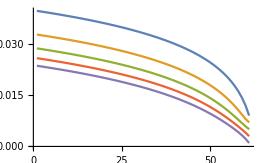

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-3*)
```

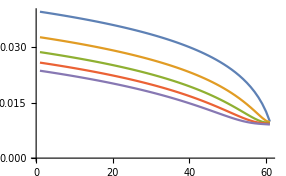

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-4*)
```

#### Numerical Experiments

```mathematica
(*Price Dynamics*)
S0=30;
𝒫=TransformedProcess[S0+σ*(W[t]),{W\[Distributed]WienerProcess[]},t];
TWAP[price_]:=MovingMap[Mean,price,price["PathLength"],None]
```

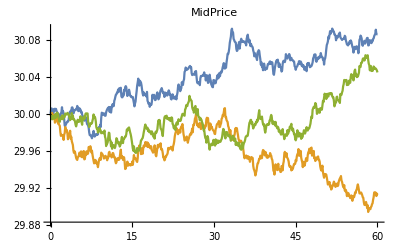
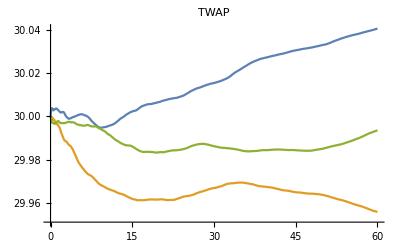

```mathematica
With[{data = RandomFunction[𝒫,{0,T,0.1},3]},
{ListLinePlot[data,PlotRange->All,PlotLabel->"MidPrice"], ListLinePlot[TWAP[data],PlotLabel->"TWAP"]}]
```

```mathematica
fillProb[δ_]:=ⅇ^(-κ*δ)
```

```mathematica
fillProb[0.01]
```

0.367879

```mathematica
backTest[price_]:=Module[
{left=𝒩,
tb=Normal[price][[1]],
depth,
time,
mPrice,
postPrice,
fillQ,
depthHis={},
inventoryHis={},
trdHis={},
priceHis={},
MOs=0},

Do[
{
AppendTo[priceHis,tb[[idx]]];
time=tb[[idx]][[1]];
mPrice=tb[[idx]][[2]];
depth=δ[time,left];
AppendTo[depthHis,{time,depth}];
If[left>0,postPrice=mPrice+depth;
fillQ=RandomVariate[BernoulliDistribution[fillProb[depth]]];
If[fillQ==1,AppendTo[trdHis,{time,postPrice}]];
left-=fillQ;];
AppendTo[inventoryHis,{time,left}];
};
If[left>0&&idx== Length@tb,
AppendTo[inventoryHis,{tb[[idx]][[1]], 0}];AppendTo[trdHis,{tb[[idx]][[1]],tb[[idx]][[2]]}];MOs=left;left=0;];
If[left==0,Break[]];,
{idx,1,Length@tb}];
Association[
"depth"-> TemporalData[depthHis],
"inventory"-> TemporalData[inventoryHis],
"trade"-> TemporalData[trdHis],
"price"-> TemporalData[priceHis],
"MOs"-> MOs]
]
```

<|depth→TemporalData[…],inventory→TemporalData[…],trade→TemporalData[…],price→TemporalData[…],MOs→0|>

ListLinePlot::lpn: 0. is not a list of numbers or pairs of numbers.

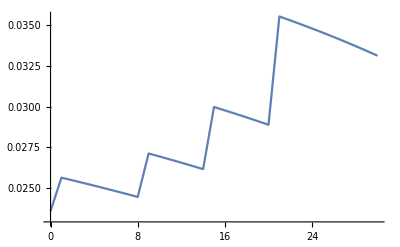
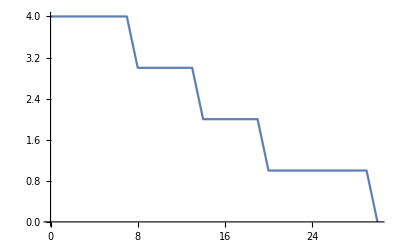
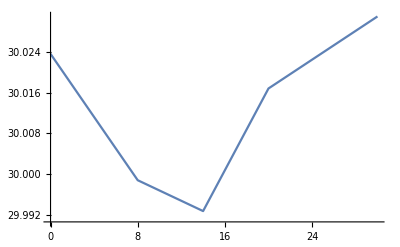
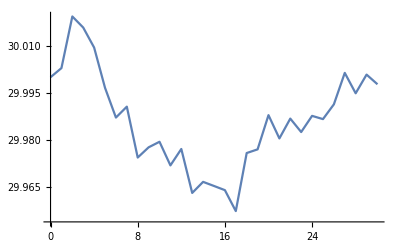
<|depth→-Graphics-,inventory→-Graphics-,trade→-Graphics-,price→-Graphics-,MOs→ListLinePlot[0]|>

```mathematica
dt = RandomFunction[𝒫,{0,T-1,1},1];
res=backTest[dt]
Map[ListLinePlot,res]
```

## 8.4 Liquidation with Limit and Market Orders

```mathematica
Clear["Global`*"]
```

Simulation Params

```mathematica
ξ=0.005;(*half spread*)
T=60;
𝒩=10;
λ=50/60;
κ=100;
S0=30;
σ=0.01;
α=0.001;
ϕ=10^-3;

𝒫=TransformedProcess[S0+σ*(W[t]),{W\[Distributed]WienerProcess[]},t];
```

```mathematica
AC[t_]:=Block[{k,ϕ2,α,b,p,γ},
(p*ⅇ^(γ*(T-t))-ⅇ^(-γ*(T-t)))/(p*ⅇ^(γ*T)-ⅇ^(-γ*T))*𝒩/.{p-> 1(*(α-1/2 b+√(k*ϕ2))/(α-1/2 b-√(k*ϕ2))*),γ-> √(ϕ2/k)}/.{k-> 0.001,ϕ2-> 10^-5,b-> 0,α-> +∞}]
```

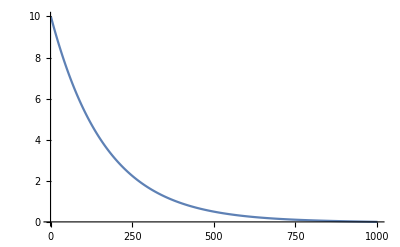

```mathematica
ListLinePlot@Table[AC[i],{i,Subdivide[0,T,1000]}]
```

```mathematica
(*terminal liquidation penalty*)
ℓ[q_]:=q*(ξ+α*q)
```

```mathematica
ω[t_/;t== T,q_/;0≤ q≤ 𝒩]:=ⅇ^(-κ*ℓ[q])
ω[t_,q_/;q==0]:=ⅇ^(-κ*ϕ*∫_t^T AC[u]^2 ⅆu)
```

```mathematica
N@First@Differences@Subdivide[0,T,3000]
```

0.02

```mathematica
fdmSolve[t_,dt_,q_]:=Module[
{timeline,
mat,
len,
trigger,
triggerIdx},

timeline=Range[0,t,dt];
len=Length@timeline;
mat=ConstantArray[0,{q+1,len}];
mat⟦1⟧=ω[#,0]&/@timeline;
mat⟦All,-1⟧=ω[t,#]&/@Range[q,0,-1];
trigger=ConstantArray[0,{q+1,len}];
trigger⟦1,-1⟧=1;
Do[
mat⟦2;;-1,i⟧=
mat⟦2;;-1,i+1⟧-
dt*κ*ϕ*Power[Range[1,q]-AC[timeline⟦i+1⟧],2]*mat⟦2;;-1,i+1⟧+
dt*ⅇ^-1*λ*mat⟦1;;-2,i+1⟧;
triggerIdx=ⅇ^(-κ*ξ)*mat⟦1;;-2,i⟧>mat⟦2;;-1,i⟧//Thread//Boole;
trigger⟦2;;-1,i⟧=triggerIdx;
mat⟦2;;-1,i⟧=MapThread[Max,{ⅇ^(-κ*ξ)*mat⟦1;;-2,i⟧,mat⟦2;;-1,i⟧}];
,{i,Reverse@Range@(len-1)}];
{mat, trigger}
]

findTrigger[triggerMat_,time_]:=
Reverse@time[[DeleteCases[Table[
With[{row=triggerMat[[idxQ]]},
SelectFirst[
Range[Length@row],
row[[#]]==1&]],{idxQ,Length@triggerMat}],_Missing]]]
```

```mathematica
{mat,trigger}=fdmSolve[T,0.01,𝒩];
```

```mathematica
ListPlot3D@mat
```

-Graphics3D-

```mathematica
timeline=Range[0,T,0.01];
moSignals=findTrigger[trigger,timeline]
```

{0.96,2.21,3.66,5.4,7.57,10.46,14.76,22.95,55.77,59.99,60.}

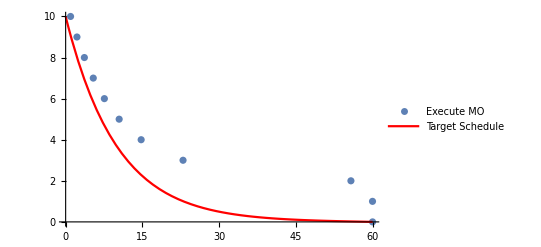

```mathematica
Show[ListPlot[Transpose@{moSignals,Reverse@Range[0,𝒩]},PlotLegends->{"Execute MO"}],Plot[AC[t],{t,0,T},PlotStyle->Red,PlotLegends->{"Target Schedule"}]]
```